## Musings as I tap out far too late : I cannot understand the results we get from the pre - window polarimetry. I tried again and again - the result are consistent. Please have a play with this notebook, see if you can reproduce a curve that looks like the contrast we get from the optics ...

Polarization sketchbook

In this notebook, I explore the representations and measurements of the polarization of light.

### Jones calculus

The electric field of a purely polarized light ray at a point in space can be expressed as the Jones vector.
In the Jones calculus, we have the following optical elements, with angles relative to the horizontal:

```mathematica
R[θ_] := {{Cos[θ],Sin[θ]},
	{-Sin[θ],Cos[θ]}};
QWP[θ_]:=E^(-ⅈ π/4){{Cos[θ]^2+ⅈ Sin[θ]^2,(1-ⅈ)Sin[θ]Cos[θ]},
			{(1-ⅈ)Sin[θ]Cos[θ],Sin[θ]^2+ⅈ Cos[θ]^2}};
HWP[θ_]:= E^(-ⅈ π/2){{Cos[θ]^2- Sin[θ]^2,2Sin[θ]Cos[θ]},
			{2Sin[θ]Cos[θ],Sin[θ]^2-Cos[θ]^2}};
HPol  = {{1,0},{0,0}};
```

And some useful functions:

```mathematica
ModSquare[x_]:=Conjugate[x]*x;
Commute[A_,B_] := Dot[A,B] - Dot[B,A];
Eye[n_] := Table[DiracDelta[i-j],{i,1,n},{j,1,n}];
Zero[n_]:= ConstantArray[0,{n,n}];
$Assumptions = {Subscript[r, x],Subscript[r, y],Subscript[ϕ, x],Subscript[ϕ, y]} ∈ Reals;
```

The general form of a Stokes vector is

```mathematica
E0 = {Subscript[r, x] E^(ⅈ Subscript[ϕ, x]),Subscript[r, y] E^(ⅈ Subscript[ϕ, y])};
```

Where the components are the complex field amplitudes of a plane wave propagating in the z direction.

Let's take a look at the setup in our experiment. We have light that is transmitted through a PBS - which we assume prepares it horizontally polarized light.
First, let’s put it through a linear polarizer whose angle we can vary, and look at the transmitted power:

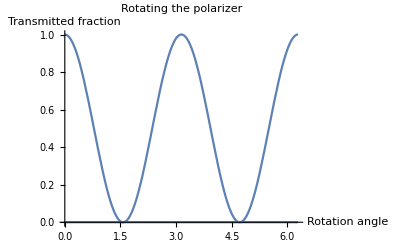

```mathematica
beamIn = {1,0};
beamOut[θ_] := Dot[HPol,R[θ],beamIn];
Plot[ModSquare[beamOut[θ]],{θ,0,2π},AxesLabel->{"Rotation angle","Transmitted fraction"},PlotLabel->"Rotating the polarizer"]
```

What if we insert a half-wave plate after the first polarizer?

```mathematica
beamAfterHWP[θ_,ϕ_] := Dot[HPol,R[θ],HWP[ϕ],beamIn];
Manipulate[Plot[ModSquare[beamAfterHWP[θ,ϕ][[1]]],{θ,0,2π},PlotLabel->"Rotating the HWP",AxesLabel->{"Polarizer angle","Transmitted power"}],{{ϕ,0,"HWP angle"},0,2π}]
```

This shouldn’t be surprising; all we’re doing is rotating the plane of polarization, which induces a phase in the output of the polarizer. Note the π period - the polarizer is sensitive only to polarization angle, not sign. Notice also that the amplitude always oscillates around 0.5.

```mathematica
Plot3D[ModSquare[beamAfterHWP[θ,ϕ][[1]]],{θ,0,2π},{ϕ,0,2π},PlotLabel->"Two-angle surface plot",AxesLabel->Automatic]
```

-Graphics3D-

What if we add a quarter wave plate? Unsurprisingly, these operations do not commute in general!

```mathematica
beamAfterHWPandQWP[θ_,ϕ1_,ϕ2_]:=Dot[R[θ],QWP[ϕ2],HWP[ϕ1],beamIn];
beamAfterQWPandHWP[θ_,ϕ1_,ϕ2_]:=Dot[R[θ],HWP[ϕ1],QWP[ϕ2],beamIn];
comm1=Commute[Dot[QWP[ϕ2],HWP[ϕ1]],Dot[HWP[ϕ1],QWP[ϕ2]]]//FullSimplify//TraditionalForm
```

(2 ⅈ sin(2 ϕ1) sin(2 ϕ1-2 ϕ2) | -2 ⅈ cos(2 ϕ1) sin(2 ϕ1-2 ϕ2)
-2 ⅈ cos(2 ϕ1) sin(2 ϕ1-2 ϕ2) | -2 ⅈ sin(2 ϕ1) sin(2 ϕ1-2 ϕ2))

In our setup, the half wave plate comes first (with the reversed order shown for comparison)

```mathematica
Grid[Manipulate[
{Plot[ModSquare[beamAfterHWPandQWP[θ,ϕ1,ϕ2][[1]]],{θ,0,2π},PlotRange->{{0,2π},{0,1}},
PlotLabel->"QWP after HWP (our optics)",AxesLabel->{"Transmitted power","Polarizer angle"},ImageSize->500],
Plot[ModSquare[beamAfterQWPandHWP[θ,ϕ1,ϕ2][[1]]],{θ,0,2π},PlotRange->{{0,2π},{0,1}},
PlotLabel->"QWP before HWP",AxesLabel->{"Transmitted power","Polarizer angle"},ImageSize->500]},
{{ϕ1,0,"HWP angle"},0,2π},{{ϕ2,0,"QWP angle"},0,2π}]]
```

Grid[]

Notice that:
	• The amplitude oscillates again around 0.5
	• rotating the half wave plate in our optics just rotates the amplitude of the transmission. 
	• Turning the quarter wave plate cycles the amplitude and induces a phase.
If the light is completely circularly polarized by the QWP, then the transmitted ratio is always 0.5:

```mathematica
ModSquare[beamAfterHWPandQWP[θ,0,π/4][[1]]]//FullSimplify
```

1/2 ⅇ^(-2 ⅈ (θ-Re[θ]))

What if our light had some circular component to it?

```mathematica
circBeamIn = Dot[QWP[π/3],beamIn];
circAfterOptics[θ_,ϕ1_,ϕ2_] := Dot[R[θ],QWP[ϕ2],HWP[ϕ1],circBeamIn];
Manipulate[
Plot[ModSquare[circAfterOptics[θ,ϕ1,ϕ2][[1]]],{θ,0,2π},PlotRange->{{0,2π},{0,1}},
PlotLabel->"QWP after HWP (our optics)",AxesLabel->{"Transmitted power","Polarizer angle"},ImageSize->500],
{{ϕ1,0,"HWP angle"},0,2π},{{ϕ2,0,"QWP angle"},0,2π}]
```

This all smells a bit mysterious now, but it becomes a bit clearer when we start looking at another geometric picture of polarization.

#### Coherence matrices & the Pauli algebra

Notice that by moving to the rotating frame with phase ϕ' = (ϕ_x-ϕ_y)/2 we can rewrite the Jones vector as

```mathematica
E1 = E^(-ⅈ (Subscript[ϕ, x]+Subscript[ϕ, y])/2)E0//FullSimplify//MatrixForm
```

(ⅇ^(1/2 ⅈ (ϕ_x-ϕ_y)) r_x
ⅇ^(-1/2 ⅈ (ϕ_x-ϕ_y)) r_y)

Denoting the phase difference ϕ_x-ϕ_y=ϕ,we have a (unit) Jones vector written as (r_x e^(ⅈ ϕ/2),r_y e^(-ⅈϕ/2))

We can define the coherence matrix χ from the Jones vector by taking its outer product with itself;

```mathematica
χ[J_]:= KroneckerProduct[Conjugate[J],J];
normχ[χ_]:=χ/Tr[χ]
χ0=χ[E0];χ0//MatrixForm//FullSimplify
```

(r_x^2 | ⅇ^(-ⅈ (ϕ_x-ϕ_y)) r_x r_y
ⅇ^(ⅈ (ϕ_x-ϕ_y)) r_x r_y | r_y^2)

Notice that the intensity of the light is now given by the diagonal sum (the trace) of the coherence matrix, and the relative phase between the orthogonal components is encoded in the off-diagonal elements (also known as coherences)

```mathematica
ConjugateTranspose[χ[E0]]-χ[E0]==Zero[2]
```

True

The action of a series of linear optics Ω on an initial beam χ is given by the conjugate action

```mathematica
OpticArray[Ω_,χ_]:=Dot[ConjugateTranspose[Ω],χ,Ω]
```

Moreover, the coherence matrix is Hermitian!Therefore, we can write the coherence matrix in a convenient basis of Hermitian operators
χ = α_i σ^i
written using Einstein notation, where we fix the σ^i to be the Pauli operators,

```mathematica
Table[PauliMatrix[k]//MatrixForm,{k,0,3}]
```

{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

and α is a 3-vector. We then have a natural embedding of the coherence matrix into 3-space by the vector α.

We can express this in the Pauli basis by taking the matrix inner product with each of the Pauli matrices;

```mathematica
MatrixInner[A_,B_]:=Tr[Dot[ConjugateTranspose[A],B]];
pauliRep[χ_]:=Table[MatrixInner[χ,PauliMatrix[k]],{k,0,3}];
pauliRep[χ0]//MatrixForm//FullSimplify
```

(r_x^2+r_y^2
2 Cos[ϕ_x-ϕ_y] r_x r_y
2 Sin[ϕ_x-ϕ_y] r_x r_y
r_x^2-r_y^2)

Where the latter three elements are the components of a and the first is the total intensity. For horizontally polarized light, we fix r_y=0. We can normalize the coherence matrix by dividing through by the total intensity (the trace of the coherence matrix),

```mathematica
normalRep[χ_]:=pauliRep[χ]/Tr[χ];
normalRep[χ0]//MatrixForm//FullSimplify
```

(1
(2 Cos[ϕ_x-ϕ_y] r_x r_y)/(r_x^2+r_y^2)
(2 Sin[ϕ_x-ϕ_y] r_x r_y)/(r_x^2+r_y^2)
-1+(2 r_x^2)/(r_x^2+r_y^2))

returning a normalized 3 - vector

```mathematica
α[χ_]:=pauliRep[χ][[2;;4]];
α[χ0]//MatrixForm//FullSimplify
```

(2 Cos[ϕ_x-ϕ_y] r_x r_y
2 Sin[ϕ_x-ϕ_y] r_x r_y
r_x^2-r_y^2)

Let’s consider some examples.

```mathematica
BlochSphere = {{Opacity[0.5],Sphere[]},{EdgeForm[{Dashed,Black}],FaceForm[None],
Cylinder[{{0,0,-.001},{0,0,.001}}]},
{Line[{{0,0,0},{1,0,0}}]},{Line[{{0,0,0},{0,1,0}}]},{Line[{{0,0,0},{0,0,1}}]},
{Line[{{0,0,0},{-1,0,0}}]},{Line[{{0,0,0},{0,-1,0}}]},{Line[{{0,0,0},{0,0,-1}}]},
Arrow[{{1,0,0},{1.3,0,0}}],Arrow[{{0,1,0},{0,1.3,0}}],Arrow[{{0,0,1},{0,0,1.3}}],
Text[Style["+",18],{1.4,0,0}],Text[Style["σ^-",18],{0,1.4,0}],Text[Style["H",18],{0,0,1.4}],
Text[Style["-",18],{-1.4,0,0}],Text[Style["σ^+",18],{0,-1.4,0}],Text[Style["V",18],{0,0,-1.4}]
}; (*Graphics primitive for the bloch sphere*)
```

```mathematica
showBlochVector[α_]:=Graphics3D[{BlochSphere,
Text[Style["r",18,Red],.5 α],{Red,Arrow[{{0,0,0},α}]},
{Dashed,Line[{α,{α[[1]],0,0}}]},{Dashed,Line[{α,{0,α[[2]],0}}]},{Dashed,Line[{α,{0,0,α[[3]]}}]},
{Black,Sphere[{{α[[1]],0,0},{0,α[[2]],0},{0,0,α[[3]]}},0.03]}
},Boxed->False,ImageSize->600]
```

This representation has a natural connection back to the familiar polarizers: The transmitted and reflected outputs of a (linear or circular) polarizer are the projections onto a 3-vector and its orthogonal complement, respectively. The magnitude of the projection onto a particular vector gives the contrast one would observe between the transmitted and reflected components, (P_trans-P_reflected)/P_Total. Passing the light through a polarizer whose projective axis is orthogonal to the coherence vector has no contrast: The input and output powers will be the same, and the  contrast is zero. This is the case when passing circularly polarized light through a linear polarizer, for example, as shown below. This is a simulation of the expected behaviour in our experiment.

```mathematica
rotateLinPolarizer[Π_,χ_,θ_]:=OpticArray[Dot[PauliMatrix[3],R[θ],Π],χ];
```

```mathematica
inputBeam =normχ[χ[{1,-0.1ⅈ}]];
Optics[γ_,ϕ_]:= Dot[QWP[γ],HWP[ϕ]];
 Manipulate[a=OpticArray[Optics[γ,ϕ],inputBeam/Tr[inputBeam]];
line1={Dashed,Line[{{0,0.5},{2π,0.5}}]};
Grid[{{Text["Input light"],Text["Transformed light"]},
{{showBlochVector[α[inputBeam]]/.PlotLabel->"test"},showBlochVector[α[a]],
Plot[rotateLinPolarizer[HPol,a,θ],{θ,0,2π},ImageSize->400,PlotRange->{0,1},PlotLabel->"Horizontal Polarizer transmission",AxesLabel->{"Polarizer angle","Transmitted fraction"},Epilog->line1]
}
}],{{ϕ,0,"HWP angle"},0,2π},{{γ,π/4,"QWP angle"},0,2π}]
```

The action of a half wave plate is simple; it rotates the polarization around the circular axis, mixing horizontal and linear components. The quarter wave plate is a little different. Below, observe the arc traced out across the Bloch sphere by a rotating QWP, when given an input vector:

```mathematica
traverseQWP[χ_,θ_]:=α[OpticArray[QWP[θ],χ]];
```

```mathematica
Manipulate[
beamIn = χ[{Cos[θ],Sin[θ]*E^(ⅈ ϕ)}];
Show[{Graphics3D[BlochSphere],ParametricPlot3D[traverseQWP[beamIn,θ1],{θ1,0,2π}]},ImageSize->500,Boxed->False],{θ,0,2π},{ϕ,0,2π}]
```

Seriously, what is that guy doing?

#### Connection to our observations

Our task is to determine the polarization state of an unknown beam in such a manner that is robust to errors. At the very least, we want to determine the degree of circularity in the polarization state of the light entering the chamber. At our disposal, we have a HWP followed by a QWP and then a linear polarizer, with variable orientation. Conveniently, the fast axes of both waveplates are marked. Notice that the degree of circular polarization sets the minimum achievable contrast. Interestingly, it seems that maximum contrast can always be retrieved with our setup, so the aim of the game is to find:

A relation (analytic, preferably) between the degree of circular polarization and the minimum contrast

A measure of the minimum contrast. Measuring this directly is prone to error from instrumental noise. Instead, one can fit a sine curve to the contrast data for a better estimate!

This is all assuming that the waveplates play nicely! Alternatively, one could ask how circular the light is after it’s passed the waveplates. In this case, all we can do is measure the contrast for a fixed set of waveplate angles - noting that the HWP should have no effect!

#### Mixed polarization

```mathematica
beamIn = normχ[χ[{1,1+1ⅈ}]];
Manipulate[Grid[{Show[{showBlochVector[α[beamIn]],showBlochVector[α[OpticArray[QWP[γ],beamIn]]],ParametricPlot3D[traverseQWP[beamIn,θ],{θ,0,2π}]},ImageSize->500,Boxed->False],
Plot[ModSquare[traverseQWP[beamIn,θ][[3]]],{θ,0,2π},PlotLabel->"Horizontal polarizer contrast",AxesLabel->{"QWP angle","Contrast"},ImageSize->500,PlotRange->{-1,1}]}],{γ,0,2π}]
```